这里p是51个已知的梅森质数指标。

```mathematica
p={2,3,5,7,13,17,19,31,61,89,107,127,521,607,1279,2203,2281,3217,4253,4423,9689,9941,11213,19937,21701,23209,44497,86243,110503,132049,216091,756839,859433,1257787,1398269,2976221,3021377,6972593,13466917,20996011,24036583,25964951,30402457,32582657,37156667,42643801,43112609,57885161,74207281,77232917,82589933}
```

{2,3,5,7,13,17,19,31,61,89,107,127,521,607,1279,2203,2281,3217,4253,4423,9689,9941,11213,19937,21701,23209,44497,86243,110503,132049,216091,756839,859433,1257787,1398269,2976221,3021377,6972593,13466917,20996011,24036583,25964951,30402457,32582657,37156667,42643801,43112609,57885161,74207281,77232917,82589933}

2.19233×10^7

```mathematica
DistributionFitTest[p,Automatic,"HypothesisTestData"]["TestDataTable",All]
```

```mathematica
Ratios[p]//N
```

{1.5,1.66667,1.4,1.85714,1.30769,1.11765,1.63158,1.96774,1.45902,1.20225,1.18692,4.10236,1.16507,2.10708,1.72244,1.03541,1.41035,1.32204,1.03997,2.19059,1.02601,1.12795,1.77803,1.08848,1.06949,1.91723,1.93818,1.2813,1.19498,1.63645,3.50241,1.13556,1.46351,1.11169,2.1285,1.01517,2.30775,1.93141,1.55908,1.14482,1.08023,1.1709,1.07171,1.14038,1.14768,1.01099,1.34265,1.28197,1.04077,1.06936}

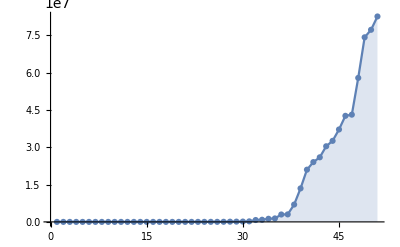

```mathematica
ListPlot[p,Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
p41=Select[p,Mod[#,4]==1&]
TwoSquares[n_]=PowersRepresentations[n,2,2];
TwoSquares/@p41
```

{5,13,17,61,89,521,2281,3217,4253,9689,9941,11213,19937,21701,23209,44497,132049,859433,1398269,2976221,3021377,6972593,13466917,30402457,32582657,42643801,43112609,57885161,74207281,77232917,82589933}

{{{1,2}},{{2,3}},{{1,4}},{{5,6}},{{5,8}},{{11,20}},{{16,45}},{{9,56}},{{38,53}},{{35,92}},{{70,71}},{{67,82}},{{76,119}},{{26,145}},{{40,147}},{{64,201}},{{120,343}},{{187,908}},{{610,1013}},{{1189,1250}},{{244,1721}},{{352,2617}},{{2241,2906}},{{3291,4424}},{{3536,4481}},{{285,6524}},{{3880,5297}},{{2444,7205}},{{2716,8175}},{{2329,8474}},{{5122,7507}}}

```mathematica
p43=Select[p,Mod[#,4]==3&]
```

```mathematica
{3,7,19,31,107,127,607,1279,2203,4423,86243,110503,216091,756839,1257787,20996011,24036583,25964951,37156667}
Table[PowersRepresentations[n,3,2],{n,p43}]；
```

{3,7,19,31,107,127,607,1279,2203,4423,86243,110503,216091,756839,1257787,20996011,24036583,25964951,37156667}

```mathematica
Table[{y=Floor@Sqrt@x,ModularInverse[y,x],z=Ceiling@Sqrt@x,ModularInverse[z,x]},{x,p}]
```

ModularInverse::ninv: 2 不是不可逆模 2.

{{1,1,2,ModularInverse[2,2]},{1,1,2,2},{2,3,3,2},{2,4,3,5},{3,9,4,10},{4,13,5,7},{4,5,5,4},{5,25,6,26},{7,35,8,23},{9,10,10,9},{10,75,11,39},{11,104,12,53},{22,450,23,68},{24,430,25,170},{35,402,36,604},{46,1772,47,375},{47,728,48,1093},{56,2700,57,2314},{65,3795,66,1611},{66,4356,67,4357},{98,8206,99,5970},{99,7029,100,3877},{105,4592,106,8780},{141,10322,142,19235},{147,20520,148,5132},{152,8398,153,21237},{210,29029,211,9279},{293,8536,294,47815},{332,70895,333,14601},{363,12732,364,111371},{464,73117,465,27418},{869,391048,870,235751},{927,190058,928,302839},{1121,301824,1122,402447},{1182,718062,1183,37823},{1725,2361998,1726,1739865},{1738,655385,1739,2753814},{2640,1856717,2641,533307},{3669,1460843,3670,6960965},{4582,12055981,4583,16936996},{4902,6908924,4903,14280760},{5095,1905965,5096,2124683},{5513,1626832,5514,22622648},{5708,24676739,5709,6614696},{6095,16380634,6096,10904409},{6530,19388889,6531,35546295},{6566,3578491,6567,25629911},{7608,39312911,7609,45987094},{8614,65222118,8615,19372278},{8788,64849988,8789,55835471},{9087,26784696,9088,20020425}}

```mathematica
(*二次剩余*)
Table[ResourceFunction["QuadraticResidues"][x],{x,{7,13,17,19,31,61,89,107,127,521,607,1279}}]
```

{{0,1,2,4},{0,1,3,4,9,10,12},{0,1,2,4,8,9,13,15,16},{0,1,4,5,6,7,9,11,16,17},{0,1,2,4,5,7,8,9,10,14,16,18,19,20,25,28},{0,1,3,4,5,9,12,13,14,15,16,19,20,22,25,27,34,36,39,41,42,45,46,47,48,49,52,56,57,58,60},{0,1,2,4,5,8,9,10,11,16,17,18,20,21,22,25,32,34,36,39,40,42,44,45,47,49,50,53,55,57,64,67,68,69,71,72,73,78,79,80,81,84,85,87,88},{0,1,3,4,9,10,11,12,13,14,16,19,23,25,27,29,30,33,34,35,36,37,39,40,41,42,44,47,48,49,52,53,56,57,61,62,64,69,75,76,79,81,83,85,86,87,89,90,92,99,100,101,102,105},{0,1,2,4,8,9,11,13,15,16,17,18,19,21,22,25,26,30,31,32,34,35,36,37,38,41,42,44,47,49,50,52,60,61,62,64,68,69,70,71,72,73,74,76,79,81,82,84,87,88,94,98,99,100,103,104,107,113,115,117,120,121,122,124},{0,1,2,4,5,8,9,10,11,13,16,18,20,21,22,25,26,29,31,32,36,37,40,42,44,45,47,49,50,51,52,53,55,57,58,59,62,64,65,69,71,72,74,80,81,83,84,88,90,94,97,98,99,100,101,102,104,105,106,110,113,114,116,117,118,119,121,123,124,125,127,128,129,130,133,138,142,143,144,145,148,151,155,160,161,162,166,168,169,176,180,183,185,188,189,194,196,197,198,199,200,201,202,204,208,210,211,212,219,220,225,226,228,231,232,233,234,235,236,237,238,242,245,246,248,250,254,255,256,258,260,261,263,265,266,267,271,273,275,276,279,283,284,285,286,287,288,289,290,293,295,296,301,302,309,310,311,313,317,319,320,321,322,323,324,325,327,332,333,336,338,341,345,352,353,355,359,360,361,366,370,373,376,377,378,379,383,388,391,392,393,394,396,397,398,400,402,403,404,405,407,408,411,415,416,417,419,420,421,422,423,424,427,431,433,437,438,440,441,447,449,450,452,456,457,459,462,463,464,466,468,469,470,471,472,474,476,477,479,481,484,485,489,490,492,495,496,499,500,501,503,505,508,510,511,512,513,516,517,519,520},{0,1,2,4,7,8,9,11,13,14,15,16,18,19,22,25,26,28,30,32,36,38,41,43,44,47,49,50,51,52,53,56,60,61,63,64,69,71,72,73,76,77,79,81,82,85,86,87,88,89,91,93,94,97,98,99,100,101,102,104,105,106,107,111,112,115,117,120,121,122,126,128,131,133,135,137,138,142,143,144,145,146,151,152,154,155,158,162,164,165,167,169,170,171,172,173,174,175,176,177,178,181,182,185,186,188,193,194,195,196,197,198,200,201,202,204,208,209,210,212,214,222,223,224,225,227,229,230,233,234,239,240,241,242,244,247,249,252,256,262,266,270,271,274,275,276,281,284,285,286,287,288,289,290,292,293,295,301,302,304,307,308,309,310,311,313,316,324,325,327,328,329,330,334,335,338,339,340,342,343,344,346,347,348,349,350,352,353,354,356,357,359,361,362,364,369,370,371,372,375,376,379,381,386,387,388,389,390,391,392,394,396,400,401,402,404,408,415,416,417,418,420,423,424,427,428,439,441,444,446,447,448,450,451,454,457,458,459,460,466,467,468,471,473,475,477,478,480,482,483,484,488,489,491,493,494,497,498,499,504,511,512,515,517,523,524,527,529,532,533,537,539,540,541,542,545,548,549,550,552,553,559,561,562,565,567,568,570,572,573,574,576,578,580,583,584,586,587,590,595,597,601,602,604},{0,1,2,4,5,7,8,9,10,14,16,17,18,20,23,25,28,32,33,34,35,36,37,39,40,41,43,45,46,47,49,50,53,56,57,59,63,64,66,68,70,72,73,74,78,79,80,81,82,83,85,86,87,90,92,93,94,97,98,100,103,106,109,112,113,114,115,118,119,121,125,126,128,132,136,140,143,144,146,148,151,153,156,158,160,161,162,163,164,165,166,167,169,170,172,174,175,179,180,181,183,184,185,186,188,193,194,195,196,197,199,200,201,205,206,207,209,212,213,215,218,224,225,226,228,229,230,231,235,236,238,239,242,245,247,250,251,252,256,259,263,264,265,267,269,272,273,277,280,281,283,285,286,287,288,289,292,293,295,296,297,301,302,303,306,307,312,313,315,316,317,319,320,321,322,324,326,328,329,330,331,332,333,334,338,340,341,343,344,347,348,350,351,358,360,361,362,365,366,368,369,370,371,372,373,376,377,381,386,387,388,389,390,391,392,393,394,395,398,399,400,402,403,405,410,411,412,413,414,415,417,418,421,423,424,425,426,430,435,436,439,441,447,448,450,452,456,458,460,461,462,463,465,467,470,471,472,476,477,478,484,485,487,490,494,500,502,504,509,511,512,513,515,518,519,521,523,526,528,529,530,531,534,538,544,545,546,551,553,554,560,561,562,565,566,567,569,570,571,572,573,574,575,576,578,581,584,586,587,589,590,592,594,595,601,602,604,605,606,607,609,612,614,624,625,626,629,630,632,633,634,638,640,642,643,644,648,651,652,656,657,658,659,660,661,662,663,664,666,668,669,671,676,679,680,681,682,683,686,688,691,694,696,697,699,700,702,711,715,716,720,721,722,723,724,727,729,730,731,732,736,737,738,739,740,742,743,744,746,747,752,754,755,757,759,762,763,765,769,771,772,773,774,776,778,780,781,782,783,784,786,787,788,790,791,793,796,797,798,799,800,804,805,806,810,811,813,815,820,822,824,825,826,828,830,833,834,835,836,837,839,841,842,845,846,847,848,850,851,852,857,859,860,863,870,871,872,873,875,878,882,883,894,895,896,897,899,900,901,904,905,912,915,916,920,922,923,924,925,926,927,930,933,934,937,940,942,943,944,952,954,956,961,965,968,969,970,971,974,975,979,980,981,985,988,989,995,997,1000,1001,1003,1004,1005,1008,1009,1011,1013,1017,1018,1019,1021,1022,1024,1025,1026,1030,1031,1033,1035,1036,1038,1039,1042,1045,1046,1047,1052,1056,1057,1058,1059,1060,1062,1063,1065,1068,1069,1071,1075,1076,1077,1081,1087,1088,1089,1090,1092,1097,1101,1102,1103,1106,1108,1111,1120,1122,1124,1125,1127,1129,1130,1132,1134,1137,1138,1140,1141,1142,1144,1145,1146,1148,1149,1150,1152,1155,1156,1157,1159,1162,1163,1168,1169,1171,1172,1174,1175,1177,1178,1180,1183,1184,1188,1190,1191,1195,1202,1203,1204,1208,1210,1212,1214,1217,1218,1219,1221,1224,1225,1227,1228,1231,1235,1237,1241,1248,1249,1250,1252,1253,1255,1257,1258,1260,1264,1266,1267,1268,1273,1276}}

2, 3,5至少有其一是其二次剩余？答案为False

```mathematica
Table[{JacobiSymbol[2,x],JacobiSymbol[3,x],JacobiSymbol[5,x],JacobiSymbol[Floor[(x-1)/2],x],JacobiSymbol[Floor[(x+1)/2],x]},{x,p}]
```

{{0,-1,-1,0,1},{-1,0,-1,1,-1},{-1,-1,0,-1,-1},{1,-1,-1,-1,1},{-1,1,-1,-1,-1},{1,-1,-1,1,1},{-1,-1,1,1,-1},{1,-1,1,-1,1},{-1,1,1,-1,-1},{1,-1,1,1,1},{-1,1,-1,1,-1},{1,-1,-1,-1,1},{1,-1,1,1,1},{1,-1,-1,-1,1},{1,-1,1,-1,1},{-1,-1,-1,1,-1},{1,1,1,1,1},{1,1,-1,1,1},{-1,-1,-1,-1,-1},{1,-1,-1,-1,1},{1,-1,1,1,1},{-1,-1,1,-1,-1},{-1,-1,-1,-1,-1},{1,-1,-1,1,1},{-1,-1,1,-1,-1},{1,1,1,1,1},{1,1,-1,1,1},{-1,1,-1,1,-1},{1,-1,-1,-1,1},{1,1,1,1,1},{-1,-1,1,1,-1},{1,1,1,-1,1},{1,-1,-1,1,1},{-1,-1,-1,1,-1},{-1,-1,1,-1,-1},{-1,-1,1,-1,-1},{1,-1,-1,1,1},{1,-1,-1,1,1},{-1,1,-1,-1,-1},{-1,-1,1,1,-1},{1,-1,-1,-1,1},{1,1,1,-1,1},{1,1,-1,1,1},{1,-1,-1,1,1},{-1,1,-1,1,-1},{1,1,1,1,1},{1,-1,1,1,1},{1,-1,1,1,1},{1,1,1,1,1},{-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1}}